```mathematica
Clear["Global`*"]
```

```mathematica
x*Integrate[BesselK[5/3,z], {z,x,Infinity}]
```

ConditionalExpression[x (1/x^(2/3)2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},x^2/4]+(π (-320+(81 2^(1/3) x^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},x^2/4])/Gamma[-1/3]))/(320 √3)), Re[x]>0&&Im[x]==0]

```mathematica
F[x_]:=x(1/x^(2/3)2^(2/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},x^2/4]+(π (-320+(81 2^(1/3) x^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},x^2/4])/Gamma[-1/3]))/(320 √3))//N;
```

```mathematica
3/10//N
```

0.3

```mathematica
F2[x_]:=x*NIntegrate[BesselK[5/3,z], {z,x,Infinity}]
```

```mathematica
F[10]//Timing
```

{0.0034,0.000192238}

```mathematica
F2[10]//Timing
```

{0.034964,0.000192238}

```mathematica
1/x*Integrate[z^2*Exp[-z]F[x/z^2],{z,0,∞}, Assumptions->{x∈Reals,z∈Reals,x>=0,z>=0}]
```

1/x Integrate[ⅇ^-z z^2 F[x/z^2],{z,0,∞},Assumptions→{x∈ℝ,z∈ℝ,x≥0,z≥0}]

```mathematica
Ii[x_]:=1/x*NIntegrate[z^2*Exp[-z]F2[x/z^2],{z,0,∞}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

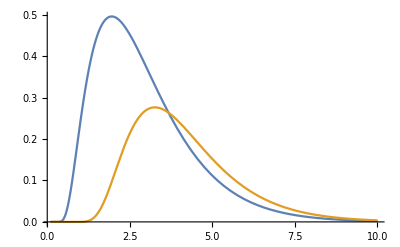

```mathematica
Plot[{z^2*Exp[-z]F2[1/z^2], z^2*Exp[-z]F2[10/z^2]}, {z,10^-1,10}]
```

```mathematica
Ii[1]
```

NIntegrate::inumri: The integrand ⅇ^-z ((2.14953 HypergeometricPFQ[{-0.333333},{-«19»,«19»},0.25/z^4])/((1/z^2)^(2/3))+0.00566812 (-320.-25.1218 «1» HypergeometricPFQ[«1»])) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,0.0000569959}}.

NIntegrate[z^2 Exp[-z] F[1/z^2],{z,0,∞}]

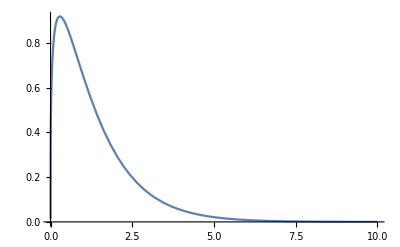

0.000192238

```mathematica
Plot[F2[x],{x,0,10}]
F2[10]
```